# TL;DL - Too Long Didn’t Listen

Keyphrase extractor from text, audio and video.

## Introduction

Example use case: Too Long Didn't Listen will extract the main phrases used throughout the lecture and will automatically tag the recorded audio files.

Another example use case : generating tags for a youtube video to attract more clicks

-Graphics-

## Importing Audio

```mathematica
path = FileNameJoin[{NotebookDirectory[], "linear_equations_snippet.mp3"}];
```

```mathematica
audio = Import[path];
```

## Speech Recognition

Extracting text from audio file using SpeechRecognize:

```mathematica
text = SpeechRecognize[audio];
```

```mathematica
text
```

Compatibility of systems of linear constraints over the set of natural numbers. Criteria of compatibility of a system of linear Diophantine equations, strict inequations, and nonstrict inequations are considered. Upper bounds for components of a minimal set of solutions and algorithms of construction of minimal generating sets of solutions for all types of systems are given. These criteria and the corresponding algorithms for constructing a minimal supporting set of solutions can be used in solving all the considered types of systems and systems of mixed types.

## Generating Vocabulary

Make all words lowercase -> convert plurals to singulars -> extract nouns and adjectives

```mathematica
generatingVocabulary[text_] :=
Module[{textLow, textNouns, plurals,singulars, rules, textSingular, textNA},
textLow = ToLowerCase[text];
textNouns = TextCases[textLow, "Noun"];
plurals = DeleteCases[If[ StringTake[#, -1]== "s", #]&/@textNouns, Null];
rules = {
RegularExpression["(\\w+)(ss)(es)"]:> "$1$2",
RegularExpression["(\\w+)(sh)(es)"]:> "$1$2",
RegularExpression["(\\w+)(ies)"]:> "$1"~~"y",
RegularExpression["(\\w+)(ss)"]:> "$1$2",
RegularExpression["(\\w+)(us)"]:> "$1$2",
RegularExpression["(\\w+)(s)"]:> "$1"
};
singulars = # -> StringReplace[#, rules]&/@plurals;
textSingular = StringReplace[textLow,singulars];
textNA = TextCases[textLow, "Adjective" | "Noun"];
List[textSingular, textNA]
];
```

```mathematica
generatedVocabulary = generatingVocabulary[text];
textSingular = generatedVocabulary[[1]];
textNA = generatedVocabulary[[2]];
vocabulary = DeleteDuplicates[textNA]
```

{compatibility,systems,linear,constraints,set,natural,numbers,criteria,system,diophantine,equations,strict,inequations,nonstrict,upper,bounds,components,minimal,solutions,algorithms,construction,sets,types,corresponding,supporting,mixed}

## Calculating Distancec and Creating Adjacency Graph

TextRank is a graph based model, and thus it requires us to build a graph. Each words in the vocabulary will serve as a vertex for graph. The words will be represented in the vertices by their index in vocabulary list.

The weighted edge matrix contains the information of edge connections among all vertices.

```mathematica
distanceCalculator[l1_, l2_] := 
Module[{tup, listSum, diff},tup = Tuples[{l1, l2}];
diff = Map[Abs[Differences[#]]&, tup];
diff =diff/.{0-> 1/$MachineEpsilon};
listSum = 1/diff;
N[Total[listSum]]
];
```

```mathematica
calculatingTextDistance[vocabulary_, textSingular_ ] :=
Module[{tupleList, positions, textDist, tupleGraph},
tupleList = Join[Subsets[vocabulary, {2}],Thread[{vocabulary, vocabulary}]];
positions= List[Position[textSingular, #[[1]]],Position[textSingular, #[[2]]]]&/@tupleList;
textDist = distanceCalculator[#[[1]], #[[2]]]&/@positions;
tupleGraph = Graph[UndirectedEdge@@@tupleList,EdgeWeight -> Flatten[textDist],VertexLabels->"Name"]
];
```

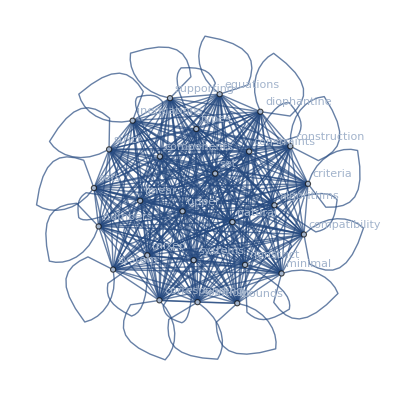

```mathematica
tupleGraph = calculatingTextDistance[vocabulary, textNA]
```

## Scoring Vocabulary

The formula used for scoring a vertex represented by i is:
score[i] = (1-d) + d x [ Summation(j) ( (weighted_edge[i][j]/inout[j]) x score[j] ) ]

```mathematica
assigningScores[matrixWeight_, vocabulary_]:=
Module[{inout, summation, score, summationMatrix, scoreAssociation},
inout = Total[matrixWeight, {2}];
summation = 0;
score  = Array[1 &, Length[vocabulary]];
For[i=1, i<= Length[vocabulary], i++, 
summation = 0;
summationMatrix = (matrixWeight /inout)* score;
summation = Total[summationMatrix[[All, i]]];
score[[i]] = 0.15 + 0.85 * summation;
];
scoreAssociation = AssociationThread[vocabulary, score]
];
```

```mathematica
matrixWeight = WeightedAdjacencyMatrix[tupleGraph];
scoreAssociation = assigningScores[matrixWeight, vocabulary]
```

<|compatibility→1.0979,systems→1.9588,linear→1.37046,constraints→0.661276,set→1.80925,natural→0.742233,numbers→0.72033,criteria→1.32351,system→0.773324,diophantine→0.801672,equations→0.792759,strict→0.755965,inequations→1.46589,nonstrict→0.782935,upper→0.786424,bounds→0.763289,components→0.700968,minimal→1.88681,solutions→1.83502,algorithms→1.39123,construction→0.753274,sets→0.722594,types→1.67754,corresponding→0.732844,supporting→0.695781,mixed→0.561697|>

```mathematica
Dataset[{Association["Vocabulary" -> "Score"],scoreAssociation}]
```

Dataset[<>]

## Phrase Partitioning

Paritioning lemmatized text into phrases using the stopwords in it as delimeters. The phrases are also candidates for keyphrases to be extracted.
Duplicates are deleted as repeating phrases\keyphrase candidates has no purpose here, anymore.

```mathematica
generatingPhrases[textSingular_, vocabulary_]:=
Module[{phraseList, wordListEmpty, wordList, phrases, uniquePhrases, thinnedLists, thinned},
phraseList = DeleteStopwords[textSingular];
wordListEmpty = StringDelete[StringSplit[phraseList, {"  ", ","}], PunctuationCharacter];
wordList = DeleteCases[DeleteCases[wordListEmpty, ""], " "];
phrases = StringReplace[StringReplace[#,(StartOfString~~Whitespace)|(Whitespace~~EndOfString):>""],Whitespace->" " ]&/@wordList;
uniquePhrases = DeleteDuplicates[phrases];
thinnedLists = If[Count[StringContainsQ[uniquePhrases, # ], True]>1, DeleteCases[uniquePhrases, #], Nothing]&/@vocabulary;
thinned = Intersection @@ thinnedLists
];
```

```mathematica
phrases = generatingPhrases[textSingular, vocabulary]
```

{algorithm,compatibility,component,considered type,considered upper bound,constructing,construction,corresponding algorithm,given,linear constraint,linear diophantine equation,minimal generating set,minimal set,minimal supporting set,mixed type,natural number criteria,nonstrict inequation,solution,solving,strict inequation,system,type,used}

## Scoring Phrases

Phrases are scored by adding the score of their members (words\text - units that were ranked by the graph algorithm):

```mathematica
phraseScore[s_, scores_]:=
Module[{l, values},
l = StringSplit[s, {" "}];
values = Values[KeyTake[scores, l]];
Total[values]
];
```

```mathematica
scoringPhrases[scoreAssociation_, phrases_]:=
Module[{keyPhrasesScore, keyPhrasesAssociation, keyPhrasesSorted},
keyPhrasesScore = phraseScore[#, scoreAssociation]&/@phrases;
keyPhrasesAssociation= AssociationThread[phrases, keyPhrasesScore];
keyPhrasesSorted = Sort[keyPhrasesAssociation, Greater]
];
```

```mathematica
keyPhrases = scoringPhrases[scoreAssociation, phrases]
```

<|minimal supporting set→4.39184,minimal set→3.69606,minimal generating set→3.69606,linear diophantine equation→2.17213,natural number criteria→2.06574,linear constraint→1.37046,compatibility→1.0979,considered upper bound→0.786424,nonstrict inequation→0.782935,system→0.773324,strict inequation→0.755965,construction→0.753274,corresponding algorithm→0.732844,mixed type→0.561697,used→0,type→0,solving→0,solution→0,given→0,constructing→0,considered type→0,component→0,algorithm→0|>

Compatibility of systems of linear constraints over the set of natural numbers. Criteria of compatibility of a system of linear Diophantine equations, strict inequations, and nonstrict inequations are considered. Upper bounds for components of a minimal set of solutions and algorithms of construction of minimal generating sets of solutions for all types of systems are given. These criteria and the corresponding algorithms for constructing a minimal supporting set of solutions can be used in solving all the considered types of systems and systems of mixed types.

```mathematica
Dataset[{Association["Vocabulary" -> "Score"],keyPhrases}]
```

Dataset[<>]

## Final Functions

#### Text

```mathematica
generateKeyWords[text_, numberOfKeyWords_]:=
Module[{generatedVocabulary, textSingular, textNA, vocabulary, tupleGraph, matrixWeight, scoreAssociation, phrases, keyPhrases},
generatedVocabulary = generatingVocabulary[text];
textSingular = generatedVocabulary[[1]];
textNA = generatedVocabulary[[2]];
vocabulary = DeleteDuplicates[textNA];
tupleGraph = calculatingTextDistance[vocabulary, textNA];
matrixWeight = WeightedAdjacencyMatrix[tupleGraph];
scoreAssociation = assigningScores[matrixWeight, vocabulary];
phrases = generatingPhrases[textSingular, vocabulary];
keyPhrases = scoringPhrases[scoreAssociation, phrases];
Take[Keys[keyPhrases], numberOfKeyWords]
];
```

#### Audio

```mathematica
generateKeyWordsAudio[audio_, numberOfKeyWords_]:=
Module[{text,generatedVocabulary, textSingular, textNA, vocabulary, tupleGraph, matrixWeight, scoreAssociation, phrases, keyPhrases},
text = SpeechRecognize[audio];
generateKeyWords[text, numberOfKeyWords]
];
```

#### Video

```mathematica
generateKeyWordsVideo[url_, numberOfKeyWords_]:=
Module[{goToYDL,extractAudio,audioPath,audio,text,generatedVocabulary, textSingular, textNA, vocabulary, tupleGraph, matrixWeight, scoreAssociation, phrases, keyPhrases},
goToYDL = "cd " <> FileNameJoin[{NotebookDirectory[], "ydl"}];
extractAudio = RunProcess[$SystemShell,All,goToYDL <>"\nyoutube-dl "<> url <>" -x --audio-format mp3 -o \"only_audio.%(ext)s\"
exit
"];
audioPath = FileNameJoin[{NotebookDirectory[], "ydl", "only_audio.mp3"}];
audio = Import[audioPath];
generateKeyWordsAudio[audio, numberOfKeyWords]
];
```

Example of Video Tag Extraction:

-Graphics-

```mathematica
generateKeyWordsVideo["https://www.youtube.com/watch?v=gtkikP3Km14", 5]
```

{electric flux,electric field,parallel component right,simple area,manageable area}

Use Case example: Comparing the keywords of 2 inauguration speeches